```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poincare/Dropbox/Documentos/DMKM/01 Lyon/Courseware/MDA/Project

```mathematica
CountryData["UN"]//Length
```

193

```mathematica
CountryData["Properties"]
```

{AdultPopulation,AgriculturalProducts,AgriculturalValueAdded,Airports,AlternateNames,AlternateStandardNames,AMRadioStations,AnnualBirths,AnnualDeaths,AnnualHIVAIDSDeaths,ArableLandArea,ArableLandFraction,Area,BirthRateFraction,BorderingCountries,BordersLengths,BoundaryLength,CallingCode,CapitalCity,CapitalLocation,CapitalLocationLink,CellularPhones,CenterCoordinates,CenterLocationLink,ChildPopulation,Classes,ClimateTypes,CoastlineLength,ConstructionValueAdded,Continent,Coordinates,Countries,CountryCode,CropsLandArea,CropsLandFraction,CurrencyCode,CurrencyName,CurrencyShortName,CurrencyUnit,CurrentAccountBalance,DeathRateFraction,Dependencies,DependencyParent,EconomicAid,ElderlyPopulation,ElectricalGridFrequency,ElectricalGridPlugImages,ElectricalGridPlugs,ElectricalGridSocketImages,ElectricalGridSockets,ElectricalGridVoltages,ElectricityConsumption,ElectricityExports,ElectricityImports,ElectricityProduction,EnvironmentalAgreements,EnvironmentalIssues,EthnicGroups,EthnicGroupsFractions,ExchangeRate,ExpenditureFractions,ExportCommodities,ExportPartners,ExportPartnersFractions,ExportValue,ExternalDebt,FemaleAdultPopulation,FemaleChildPopulation,FemaleElderlyPopulation,FemaleInfantMortalityFraction,FemaleLifeExpectancy,FemaleLiteracyFraction,FemaleMedianAge,FemalePopulation,FiscalYearDate,FixedInvestment,Flag,FlagDescription,FMRadioStations,ForeignExchangeReserves,ForeignOwnedShips,ForeignRegisteredShips,FullCoordinates,FullName,FullNativeName,FullPolygon,GDP,GDPAtParity,GDPPerCapita,GDPRealGrowth,GDPSectorFractions,GiniIndex,GovernmentConsumption,GovernmentDebt,GovernmentExpenditures,GovernmentReceipts,GovernmentSurplus,GrossInvestment,Groups,HighestElevation,HighestPoint,HIVAIDSDeathRateFraction,HIVAIDSFraction,HIVAIDSPopulation,HouseholdConsumption,ImportCommodities,ImportPartners,ImportPartnersFractions,ImportValue,IndependenceDate,IndependenceYear,IndustrialProductionGrowth,IndustrialValueAdded,InfantMortalityFraction,InfectiousDiseases,InflationRate,InternationalOrganizations,InternationalOrganizationsObserver,InternetCode,InternetHosts,InternetUsers,InventoryChange,IrrigatedLandArea,IrrigatedLandFraction,ISOName,LaborForce,LandArea,Languages,LanguagesDialects,LanguagesFractions,LargestCities,LifeExpectancy,LiteracyFraction,LowestElevation,LowestPoint,MajorIndustries,MajorPorts,MaleAdultPopulation,MaleChildPopulation,MaleElderlyPopulation,MaleInfantMortalityFraction,MaleLifeExpectancy,MaleLiteracyFraction,MaleMedianAge,MalePopulation,ManufacturingValueAdded,MaritimeClaims,MedianAge,Memberships,MerchantShips,MerchantShipsDeadWeight,MerchantShipsGross,MerchantShipTypes,MigrationRateFraction,MilitaryAgeFemales,MilitaryAgeMales,MilitaryAgePopulation,MilitaryAgeRate,MilitaryExpenditureFraction,MilitaryExpenditures,MilitaryFitFemales,MilitaryFitMales,MilitaryFitPopulation,MiscellaneousValueAdded,Name,NationalIncome,NationalityName,NativeName,NaturalGasConsumption,NaturalGasExports,NaturalGasImports,NaturalGasProduction,NaturalGasReserves,NaturalHazards,NaturalResources,OilConsumption,OilExports,OilImports,OilProduction,OilReserves,PavedAirportLengths,PavedAirports,PavedRoadLength,PhoneLines,Pipelines,Polygon,Population,PopulationGrowth,PovertyFraction,PriceIndex,RadioStations,RailwayGaugeLengths,RailwayGaugeRules,RailwayLength,RegionNames,Regions,Religions,ReligionsFractions,RoadLength,SchematicCoordinates,SchematicPolygon,SectorLaborFractions,Shape,ShortWaveRadioStations,SignedEnvironmentalAgreements,StandardName,SuffrageType,TelevisionStations,TerrainTypes,TimeZones,TotalConsumption,TotalFertilityRate,TradeValueAdded,TransportationValueAdded,UNCode,UnemploymentFraction,UNNumber,UnpavedAirportLengths,UnpavedAirports,UnpavedRoadLength,ValueAdded,WaterArea,WaterwayLength}

```mathematica
f1=Table[CountryData[CountryData[][[1]],CountryData["Properties"][[i]]],{i,Length[CountryData["Properties"]]}];
```

{1.80536×10^7,{Fruit,Lambskins,Mutton,Nuts,Opium,Sheepskins,Wheat,Wool},Missing[NotAvailable],51,{},{},21,1.03398×10^6,238866.,Missing[NotAvailable],204,AFG,0.4,4,{Total→35,Over10000Feet→1,8000To10000Feet→4,5000To8000Feet→16,3000To5000Feet→5,Under3000Feet→9},35,29800.,1.18812×10^10,0.,1200.}
 |  |  |  |

```mathematica
f2={CountryData["Properties"],f1};
```

{{AdultPopulation,AgriculturalProducts,AgriculturalValueAdded,Airports,AlternateNames,AlternateStandardNames,AMRadioStations,209,UNNumber,UnpavedAirportLengths,UnpavedAirports,UnpavedRoadLength,ValueAdded,WaterArea,WaterwayLength},{1.80536×10^7,222}}
 |  |  |  |

```mathematica
Manipulate[Transpose[f2][[i]],{i,1,Length[CountryData["Properties"]],1}]
```

Part::partw: Part 114 of Transpose[f2] does not exist.

```mathematica
(*Index of the Selected Variables *)
vars1={33,84,30,111,1,8,9,14,25,41,45,114,132,133,148,154,187,188,189,212,36,60,66,80,87,88,89,90,94,95,96,112,116,126,190,216,202,64,108,52,53,54,55,169,170,171,172,173,176,177,178,179,180,4,7,22,79,120,121,150,151,152,182,184,191,194,199,204,208,219,11,12,13,17,28,34,35,100,123,124,127,134,222(*,223*),155,156,157,158,159,160,163};
```

```mathematica
(*Prints the variable Map*)Prepend[{Range[Length[vars1]],CountryData["Properties"][[vars1]],CountryData["US",#,"Units"]&/@CountryData["Properties"][[vars1]],
Flatten[{Table["Identification",{i,3}],Table["Demographic",{i,20-4+1}],Table["Economic",{i,39-21+1}],Table["Energy",{i,53-40+1}],Table["Communication",{i,70-54+1}],Table["Geography",{i,83-71+1}],Table["Military",{i,90-84+1}]}]}ᵀ,
{"Index","Property","Unit","Group"}]//TableForm;
```

```mathematica
(*Retrieves the Selected variables of the countries of the United Nations from the Wolfram|Alpha Knowledge Base*)s1=Transpose[ParallelTable[CountryData[CountryData["UN"][[j]],CountryData["Properties"][[i]]],{i,vars1},{j,Length[CountryData["UN"]]}]];
```

Initializing Wolfram Knowledgebase connection ....

```mathematica
(*Converts Quantity objects to plain plain text*)
q1=Flatten[Position[Table[AnyTrue[QuantityQ/@(s1ᵀ[[j]]),TrueQ],{j,Length[s1ᵀ]}],True]];
For[ii=1,ii<=Length[s1],ii++,
s1[[ii,q1]]=QuantityMagnitude[s1[[ii,q1]]]
]
```

```mathematica
(*Converts Entity Object to plain text*)
s1[[All,3]]=CanonicalName[s1ᵀ[[3]]]//Quiet;
s1[[All,4]]=Map[Part[#,1]&,Normal/@s1[[All,4]]]//Quiet;
s1[[All,37]]=Part[#,1,1]&/@(Sort[#,#1[[2]]>#2[[2]]&]&/@s1[[All,37]])//Quiet;
s1[[All,38]]=CanonicalName[Part[#,1,1]&/@(Sort[#,#1[[2]]>#2[[2]]&]&/@s1[[All,38]])]//Quiet;
s1[[All,39]]=CanonicalName[Part[#,1,1]&/@(Sort[#,#1[[2]]>#2[[2]]&]&/@s1[[All,39]])]//Quiet;
```

```mathematica
s1[[All,37]]=Replace[s1[[All,37]],"Services"->"IndustryAndServices"];
s1[[All,37]]=Replace[s1[[All,37]],"Industry"->"IndustryAndServices"];
```

```mathematica
(*Signals correctly the missing Data for output*)
s1=Replace[s1,Missing["NotAvailable"][[1,1]]->Missing["NotAvailable"],2]//Quiet;
s1=Replace[s1,CanonicalName[Missing["NotAvailable"][[1,1]]]->Missing["NotAvailable"],2]//Quiet;
s1=Replace[s1,QuantityMagnitude[Missing["NotAvailable"]]->Missing["NotAvailable"],2]//Quiet;
s1=Replace[s1,QuantityMagnitude[Missing["NotApplicable"]]->Missing["NotAvailable"],2]//Quiet;
s1=Replace[s1,"NotApplicable"->Missing["NotAvailable"],2]//Quiet;
```

```mathematica
(*Takes the log base 10 of a subset of the selected variables*)log=Complement[Range[Length[s1ᵀ]],{1,2,3,21,37,38,39},{8,10,12,13,14,15,16,18,19,20,28,32,33,35,36,72,78,80,88}];
For[ii=1,ii≤Length[log],ii++,
s1[[All,log[[ii]]]]=N[Log[10,s1[[All,log[[ii]]]]]]
]
```

```mathematica
s1=Replace[s1,0.43429448190325176 Log[QuantityMagnitude[Missing["NotAvailable"]]]->Missing["NotAvailable"],2];
s1=Replace[s1,0.43429448190325176 Log[QuantityMagnitude[Missing["NotApplicable"]]]->Missing["NotAvailable"],2];
s1=Replace[s1,0.43429448190325176 Log[Missing["NotAvailable"]]->Missing["NotAvailable"],2];
s1=Replace[s1,Indeterminate->Missing["NotAvailable"],2];
```

```mathematica
(*Removes undesired countries*)s1=Select[s1,!IntersectingQ[{#[[1]]},{"CX","CC","FK",Missing["NotApplicable"],"NU","NF","PN","SJ","TK","VA","WF","SS"}]&];
```

```mathematica
(*Save binaries of the computation*)
DumpSave["s1.mx",s1];
```

```mathematica
(*Retrieve the binaries*)
<<s1.mx;
```

```mathematica
Flatten[{s1[[1,1]]}∩CountryData["G20","CountryCode"]]
```

{}

```mathematica
s1=Append[s1ᵀ,Table[({s1[[i,1]]}∩CountryData["G20","CountryCode"])[[1]],{i,Length[s1]}]]ᵀ;
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
(*Export to excel*)
Export["s1.xls",Insert[s1,CountryData["Properties"][[vars1]],1]]
```

s1.xls

```mathematica
CountryData["Properties"][[vars1]][[3]]
```

Continent

```mathematica
Manipulate[{CountryData["Properties"][[vars1]][[i]],s1ᵀ[[i]]},{i,1,Length[s1ᵀ],1}]
```

```mathematica
Prepend[{Range[Length[vars1]],CountryData["Properties"][[vars1]]}ᵀ,
{"Index","Property"}]//TableForm
```

Index | Property
1 | CountryCode
2 | FullName
3 | Continent
4 | IndependenceYear
5 | AdultPopulation
6 | AnnualBirths
7 | AnnualDeaths
8 | BirthRateFraction
9 | ChildPopulation
10 | DeathRateFraction
11 | ElderlyPopulation
12 | InfantMortalityFraction
13 | LifeExpectancy
14 | LiteracyFraction
15 | MedianAge
16 | MigrationRateFraction
17 | Population
18 | PopulationGrowth
19 | PovertyFraction
20 | TotalFertilityRate
21 | CurrencyCode
22 | ExchangeRate
23 | ExternalDebt
24 | ForeignExchangeReserves
25 | GDP
26 | GDPAtParity
27 | GDPPerCapita
28 | GDPRealGrowth
29 | GovernmentDebt
30 | GovernmentExpenditures
31 | GovernmentReceipts
32 | IndustrialProductionGrowth
33 | InflationRate
34 | LaborForce
35 | PriceIndex
36 | UnemploymentFraction
37 | SectorLaborFractions
38 | ExportPartnersFractions
39 | ImportPartnersFractions
40 | ElectricityConsumption
41 | ElectricityExports
42 | ElectricityImports
43 | ElectricityProduction
44 | NaturalGasConsumption
45 | NaturalGasExports
46 | NaturalGasImports
47 | NaturalGasProduction
48 | NaturalGasReserves
49 | OilConsumption
50 | OilExports
51 | OilImports
52 | OilProduction
53 | OilReserves
54 | Airports
55 | AMRadioStations
56 | CellularPhones
57 | FMRadioStations
58 | InternetHosts
59 | InternetUsers
60 | MerchantShips
61 | MerchantShipsDeadWeight
62 | MerchantShipsGross
63 | PavedAirports
64 | PhoneLines
65 | RadioStations
66 | RailwayLength
67 | RoadLength
68 | ShortWaveRadioStations
69 | TelevisionStations
70 | UnpavedAirports
71 | ArableLandArea
72 | ArableLandFraction
73 | Area
74 | BoundaryLength
75 | CoastlineLength
76 | CropsLandArea
77 | CropsLandFraction
78 | HighestElevation
79 | IrrigatedLandArea
80 | IrrigatedLandFraction
81 | LandArea
82 | LowestElevation
83 | WaterArea
84 | MilitaryAgeFemales
85 | MilitaryAgeMales
86 | MilitaryAgePopulation
87 | MilitaryAgeRate
88 | MilitaryExpenditureFraction
89 | MilitaryExpenditures
90 | MilitaryFitPopulation

```mathematica
Manipulate[{CountryData["Properties"][[vars1]],s1[[i]]}ᵀ//TableForm,{i,1,Length[s1],1}]
```

Part::pkspec1: The expression us cannot be used as a part specification.

Transpose::nmtx: The first two levels of {{"CountryCode", "FullName", "Continent", "IndependenceYear", "AdultPopulation", "AnnualBirths", "AnnualDeaths", "BirthRateFraction", "ChildPopulation", « 33 », "ElectricityProduction", "NaturalGasConsumption", "NaturalGasExports", "NaturalGasImports", "NaturalGasProduction", "NaturalGasReserves", "OilConsumption", "OilExports", « 40 »}, {« 1 »} ⟦ us ⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{"CountryCode", "FullName", "Continent", "IndependenceYear", "AdultPopulation", "AnnualBirths", "AnnualDeaths", « 37 », "NaturalGasExports", "NaturalGasImports", "NaturalGasProduction", "NaturalGasReserves", "OilConsumption", "OilExports", « 40 »}, « 1 »} cannot be transposed.

```mathematica
CountryData["G8"]
```

{Canada,France,Germany,Italy,Japan,United Kingdom,United States}

```mathematica
s1ᵀ[[1;;3]]ᵀ//TableForm
```

AF | Islamic Republic of Afghanistan | Asia
AL | Republic of Albania | Europe
DZ | People's Democratic Republic of Algeria | Africa
AD | Principality of Andorra | Europe
AO | Republic of Angola | Africa
AG | Antigua and Barbuda | NorthAmerica
AR | Argentine Republic | SouthAmerica
AM | Republic of Armenia | Asia
AU | Commonwealth of Australia | Oceania
AT | Republic of Austria | Europe
AZ | Republic of Azerbaijan | Asia
BS | Commonwealth of The Bahamas | NorthAmerica
BH | Kingdom of Bahrain | Asia
BD | People's Republic of Bangladesh | Asia
BB | Barbados | NorthAmerica
BY | Republic of Belarus | Europe
BE | Kingdom of Belgium | Europe
BZ | Belize | NorthAmerica
BJ | Republic of Benin | Africa
BT | Kingdom of Bhutan | Asia
BO | Plurinational State of Bolivia | SouthAmerica
BA | Bosnia and Herzegovina | Europe
BW | Republic of Botswana | Africa
BR | Federative Republic of Brazil | SouthAmerica
BN | Brunei Darussalam | Asia
BG | Republic of Bulgaria | Europe
BF | Burkina Faso | Africa
BI | Republic of Burundi | Africa
KH | Kingdom of Cambodia | Asia
CM | Republic of Cameroon | Africa
CA | Canada | NorthAmerica
CV | Republic of Cape Verde | Africa
CF | Central African Republic | Africa
TD | Republic of Chad | Africa
CL | Republic of Chile | SouthAmerica
CN | People's Republic of China | Asia
CO | Republic of Colombia | SouthAmerica
KM | Union of the Comoros | Africa
CR | Republic of Costa Rica | NorthAmerica
HR | Republic of Croatia | Europe
CU | Republic of Cuba | NorthAmerica
CY | Republic of Cyprus | Asia
CZ | Czech Republic | Europe
CD | Democratic Republic of the Congo | Africa
DK | Kingdom of Denmark | Europe
DJ | Republic of Djibouti | Africa
DM | Commonwealth of Dominica | NorthAmerica
DO | Dominican Republic | NorthAmerica
TL | Democratic Republic of Timor-Leste | Asia
EC | Republic of Ecuador | SouthAmerica
EG | Arab Republic of Egypt | Africa
SV | Republic of El Salvador | NorthAmerica
GQ | Republic of Equatorial Guinea | Africa
ER | State of Eritrea | Africa
EE | Republic of Estonia | Europe
ET | Federal Democratic Republic of Ethiopia | Africa
FJ | Republic of the Fiji Islands | Oceania
FI | Republic of Finland | Europe
FR | French Republic | Europe
GA | Gabonese Republic | Africa
GM | Republic of The Gambia | Africa
GE | Georgia | Asia
DE | Federal Republic of Germany | Europe
GH | Republic of Ghana | Africa
GR | Hellenic Republic | Europe
GD | Grenada | NorthAmerica
GT | Republic of Guatemala | NorthAmerica
GN | Republic of Guinea | Africa
GW | Republic of Guinea-Bissau | Africa
GY | Cooperative Republic of Guyana | SouthAmerica
HT | Republic of Haiti | NorthAmerica
HN | Republic of Honduras | NorthAmerica
HU | Hungary | Europe
IS | Iceland | Europe
IN | Republic of India | Asia
ID | Republic of Indonesia | Asia
IR | Islamic Republic of Iran | Asia
IQ | Republic of Iraq | Asia
IE | Ireland | Europe
IL | State of Israel | Asia
IT | Italian Republic | Europe
CI | Republic of Cote d'Ivoire | Africa
JM | Jamaica | NorthAmerica
JP | Japan | Asia
JO | Hashemite Kingdom of Jordan | Asia
KZ | Republic of Kazakhstan | Asia
KE | Republic of Kenya | Africa
KI | Republic of Kiribati | Oceania
KW | State of Kuwait | Asia
KG | Kyrgyz Republic | Asia
LA | Lao People's Democratic Republic | Asia
LV | Republic of Latvia | Europe
LB | Lebanese Republic | Asia
LS | Kingdom of Lesotho | Africa
LR | Republic of Liberia | Africa
LY | Great Socialist People's Libyan Arab Jamahiriya | Africa
LI | Principality of Liechtenstein | Europe
LT | Republic of Lithuania | Europe
LU | Grand Duchy of Luxembourg | Europe
MK | Republic of Macedonia (FYROM) | Europe
MG | Republic of Madagascar | Africa
MW | Republic of Malawi | Africa
MY | Malaysia | Asia
MV | Republic of Maldives | Asia
ML | Republic of Mali | Africa
MT | Republic of Malta | Europe
MH | Republic of the Marshall Islands | Oceania
MR | Islamic Republic of Mauritania | Africa
MU | Republic of Mauritius | Africa
MX | United Mexican States | NorthAmerica
FM | Federated States of Micronesia | Oceania
MD | Republic of Moldova | Europe
MC | Principality of Monaco | Europe
MN | Mongolia | Asia
ME | Republic of Montenegro | Europe
MA | Kingdom of Morocco | Africa
MZ | Republic of Mozambique | Africa
MM | Union of Myanmar | Asia
NA | Republic of Namibia | Africa
NR | Republic of Nauru | Oceania
NP | Federal Democratic Republic of Nepal | Asia
NL | Kingdom of the Netherlands | Europe
NZ | New Zealand | Oceania
NI | Republic of Nicaragua | NorthAmerica
NE | Republic of Niger | Africa
NG | Federal Republic of Nigeria | Africa
KP | Democratic People's Republic of Korea | Asia
NO | Kingdom of Norway | Europe
OM | Sultanate of Oman | Asia
PK | Islamic Republic of Pakistan | Asia
PW | Republic of Palau | Oceania
PA | Republic of Panama | NorthAmerica
PG | Independent State of Papua New Guinea | Oceania
PY | Republic of Paraguay | SouthAmerica
PE | Republic of Peru | SouthAmerica
PH | Republic of the Philippines | Asia
PL | Republic of Poland | Europe
PT | Portuguese Republic | Europe
QA | State of Qatar | Asia
CG | Republic of the Congo | Africa
RO | Romania | Europe
RU | Russian Federation | Asia
RW | Republic of Rwanda | Africa
KN | Federation of Saint Kitts and Nevis | NorthAmerica
LC | Saint Lucia | NorthAmerica
VC | Saint Vincent and the Grenadines | NorthAmerica
WS | Independent State of Samoa | Oceania
SM | Republic of San Marino | Europe
ST | Democratic Republic of Sao Tome and Principe | Africa
SA | Kingdom of Saudi Arabia | Asia
SN | Republic of Senegal | Africa
RS | Republic of Serbia | Europe
SC | Republic of Seychelles | Africa
SL | Republic of Sierra Leone | Africa
SG | Republic of Singapore | Asia
SK | Slovak Republic | Europe
SI | Republic of Slovenia | Europe
SB | Solomon Islands | Oceania
SO | Somalia | Africa
ZA | Republic of South Africa | Africa
KR | Republic of Korea | Asia
ES | Kingdom of Spain | Europe
LK | Democratic Socialist Republic of Sri Lanka | Asia
SD | Republic of the Sudan | Africa
SR | Republic of Suriname | SouthAmerica
SZ | Kingdom of Swaziland | Africa
SE | Kingdom of Sweden | Europe
CH | Swiss Confederation | Europe
SY | Syrian Arab Republic | Asia
TJ | Republic of Tajikistan | Asia
TZ | United Republic of Tanzania | Africa
TH | Kingdom of Thailand | Asia
TG | Togolese Republic | Africa
TO | Kingdom of Tonga | Oceania
TT | Republic of Trinidad and Tobago | NorthAmerica
TN | Tunisian Republic | Africa
TR | Republic of Turkey | Asia
TM | Turkmenistan | Asia
TV | Tuvalu | Oceania
UG | Republic of Uganda | Africa
UA | Ukraine | Europe
AE | United Arab Emirates | Asia
GB | United Kingdom of Great Britain and Northern Ireland | Europe
US | United States of America | NorthAmerica
UY | Oriental Republic of Uruguay | SouthAmerica
UZ | Republic of Uzbekistan | Asia
VU | Republic of Vanuatu | Oceania
VE | Bolivarian Republic of Venezuela | SouthAmerica
VN | Socialist Republic of Vietnam | Asia
YE | Republic of Yemen | Asia
ZM | Republic of Zambia | Africa
ZW | Republic of Zimbabwe | Africa

```mathematica
labeler[a_]:=#<>"%"&/@ToString/@N[a/Total[a],2]
```

```mathematica
PieChart[Tally[s1ᵀ[[3]]][[All,2]],ChartLegends->Placed[Tally[s1ᵀ[[3]]][[All,1]],Below],PlotLabel->CountryData["Properties"][[vars1]][[3]],ChartLabels->labeler[Tally[s1ᵀ[[3]]][[All,2]]]]
Export["f21.eps",%]
```

-Graphics-

f21.eps

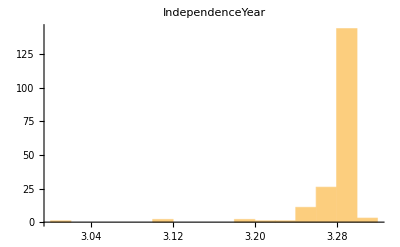
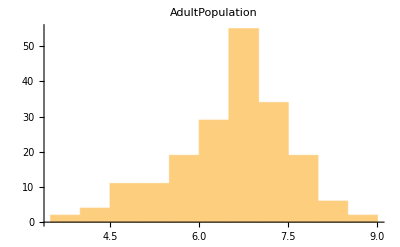
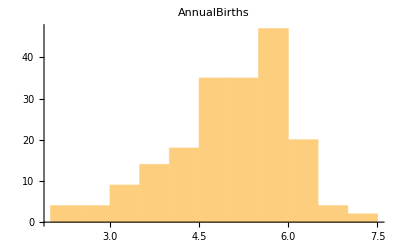
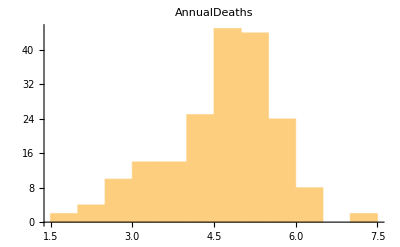
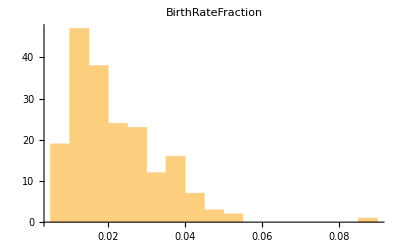
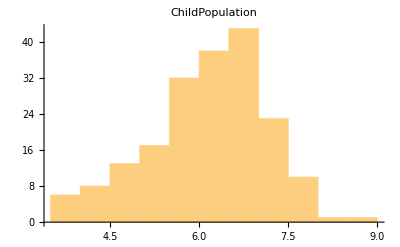
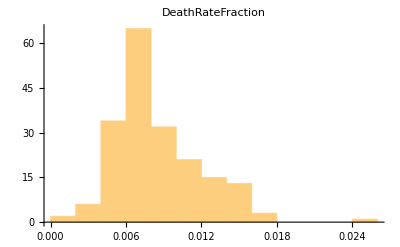
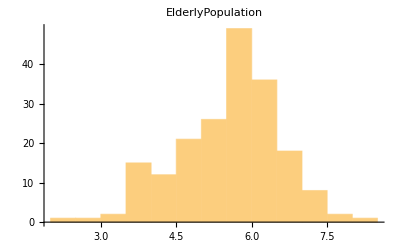

```mathematica
Table[Histogram[s1ᵀ[[i]],PlotLabel->CountryData["Properties"][[vars1]][[i]]],{i,Complement[Range[Length[s1ᵀ]],{1,2,3,21,37,38,39}]}]
```

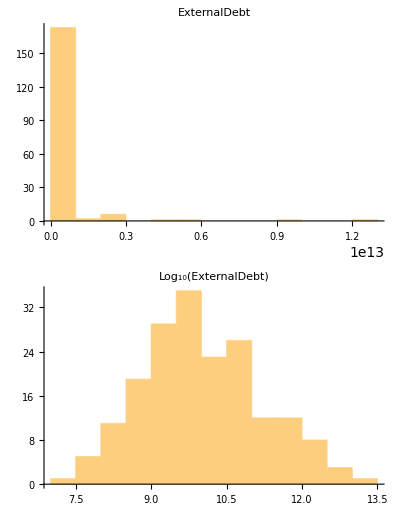

f1.eps

```mathematica
GraphicsColumn[{
Histogram[10^s1ᵀ[[23]],PlotLabel->CountryData["Properties"][[vars1]][[23]]],
Histogram[s1ᵀ[[23]],PlotLabel->Subscript[Log, 10][CountryData["Properties"][[vars1]][[23]]]]}
]
Export["f1.eps",%]
```

```mathematica
Skewness[Select[10^s1ᵀ[[23]],NumberQ]]
```

6.73181

```mathematica
Skewness[Select[s1ᵀ[[23]],NumberQ]]
```

0.319018

```mathematica
InverseCDF[ChiSquareDistribution[4],.95]
```

9.48773

```mathematica
CountryData["G10","CountryCode"]
```

{BE,CA,FR,DE,IT,JP,NL,SE,CH,GB,US}

```mathematica
Table[{s1[[i,1]]}∩CountryData["G20","CountryCode"],{i,Length[s1]}]
```

{{},{},{},{},{},{},{AR},{},{AU},{AT},{},{},{},{},{},{},{BE},{},{},{},{},{},{},{BR},{},{BG},{},{},{},{},{CA},{},{},{},{},{CN},{},{},{},{},{},{CY},{CZ},{},{DK},{},{},{},{},{},{},{},{},{},{EE},{},{},{FI},{FR},{},{},{},{DE},{},{GR},{},{},{},{},{},{},{},{HU},{},{IN},{ID},{},{},{IE},{},{IT},{},{},{JP},{},{},{},{},{},{},{},{LV},{},{},{},{},{},{LT},{LU},{},{},{},{},{},{},{MT},{},{},{},{MX},{},{},{},{},{},{},{},{},{},{},{},{NL},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{PL},{PT},{},{},{RO},{RU},{},{},{},{},{},{},{},{SA},{},{},{},{},{},{SK},{SI},{},{},{ZA},{KR},{ES},{},{},{},{},{SE},{},{},{},{},{},{},{},{},{},{TR},{},{},{},{},{},{GB},{US},{},{},{},{},{},{},{},{}}

```mathematica
Append[s1ᵀ,Table[{s1[[i,1]]}∩CountryData["G20","CountryCode"],{i,Length[s1]}]]ᵀ[[1]]
```

{AF,Islamic Republic of Afghanistan,Asia,3.28307,7.25656,6.01451,5.37815,0.0290254,7.19462,0.00670534,5.89897,0.15195,60.947,0.281,15.638,0.021,7.55173,0.0330226,0.53,4.9,AFN,1.69461,9.90309,Missing[NotAvailable],10.1031,10.3487,2.66837,0.0335009,Missing[NotAvailable],8.74896,8.42975,Missing[NotAvailable],0.212196,7.17609,139.807,0.4,Agriculture,India,Pakistan,9.00432,Missing[NotAvailable],8.,8.92376,7.47712,Missing[NotAvailable],Missing[NotAvailable],7.47712,10.695,3.69897,Missing[NotAvailable],3.64385,Missing[NotAvailable],Missing[NotAvailable],1.70757,1.32222,6.92686,0.69897,1.6721,5.69897,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],1.20412,5.66276,1.43136,Missing[NotAvailable],4.6248,0.,0.845098,1.54407,4.89154,0.119436,5.8144,3.74265,Missing[NotAvailable],3.13663,-2.67778,7485.,4.43457,0.0417031,5.8144,2.41162,Missing[NotAvailable],6.8454,6.87106,7.15945,5.87184,0.019,8.19832,6.92656,{}}

```mathematica
s1ᵀ[[1]]
```

{AF,AL,DZ,AD,AO,AG,AR,AM,AU,AT,AZ,BS,BH,BD,BB,BY,BE,BZ,BJ,BT,BO,BA,BW,BR,BN,BG,BF,BI,KH,CM,CA,CV,CF,TD,CL,CN,CO,KM,CR,HR,CU,CY,CZ,CD,DK,DJ,DM,DO,TL,EC,EG,SV,GQ,ER,EE,ET,FJ,FI,FR,GA,GM,GE,DE,GH,GR,GD,GT,GN,GW,GY,HT,HN,HU,IS,IN,ID,IR,IQ,IE,IL,IT,CI,JM,JP,JO,KZ,KE,KI,KW,KG,LA,LV,LB,LS,LR,LY,LI,LT,LU,MK,MG,MW,MY,MV,ML,MT,MH,MR,MU,MX,FM,MD,MC,MN,ME,MA,MZ,MM,NA,NR,NP,NL,NZ,NI,NE,NG,KP,NO,OM,PK,PW,PA,PG,PY,PE,PH,PL,PT,QA,CG,RO,RU,RW,KN,LC,VC,WS,SM,ST,SA,SN,RS,SC,SL,SG,SK,SI,SB,SO,ZA,KR,ES,LK,SD,SR,SZ,SE,CH,SY,TJ,TZ,TH,TG,TO,TT,TN,TR,TM,TV,UG,UA,AE,GB,US,UY,UZ,VU,VE,VN,YE,ZM,ZW}